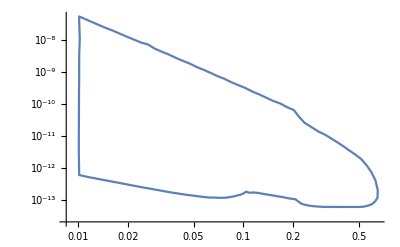

DP_NA62-dump-with-brem-collaboration.txt

```mathematica
SetDirectory[NotebookDirectory[]];
ff=Import["DP_NA62-dump-with-brem-collaboration.txt","Table"];
ff=ff[[FindShortestTour[{Log10[#[[1]]],Log10[#[[2]]]}&/@ff][[2]]]];
ListLogLogPlot[ff,Joined->True]
Export["DP_NA62-dump-with-brem-collaboration.txt",ff,"Table"]
```